## Завдання 1 пункт 1

Тут в лоб малюємо лінії за допомогою вбудованої функції вольфрам

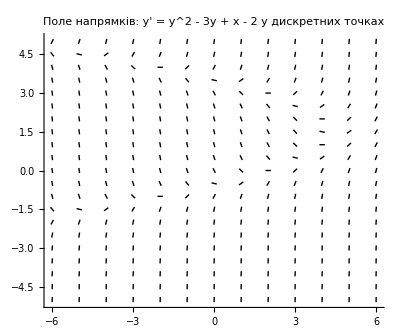

```mathematica
eq=y'[x]==y[x]^2-3*y[x]+x-2;


field=Table[Module[{x0=m,y0=n/2,slope,len=0.2},
slope=y0^2-3*y0+x0-2; 
 With[{dx=len/Sqrt[1+slope^2]},
Line[{
{x0-dx/2,y0-(dx*slope)/2},
{x0+dx/2,y0+(dx*slope)/2} }]
]
]
,{m,-6,6},
{n,-10,10}
];
fieldFlat=Flatten[field,2];
Graphics[fieldFlat,
Axes->True,
PlotRange->All,
AspectRatio->Automatic,
PlotLabel->"Поле напрямків: y' = y^2 - 3y + x - 2 у дискретних точках"
]
```

## Завдання 1, пункт 2

Тут потрібно буде схитрувати, якщо ізоклін це всі такі точки x, y в яких . То правдою буде що це всі такі точки в яких .

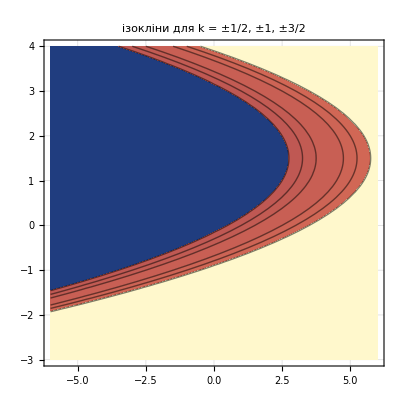

```mathematica
ContourPlot[y^2-3 y+x-2,{x,-6,6},{y,-3,4},
Contours->{-3/2,-1,-1/2,1/2,1,3/2},
ContourStyle->Thick,
PlotLegends->"Expressions",
GridLines->Automatic,
PlotLabel->"ізокліни для k = ±1/2, ±1, ±3/2"
]
```

## Завдання 1, пункт 2 (білий фон)

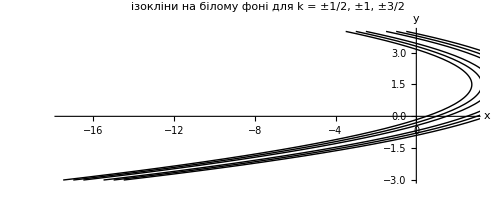

```mathematica
kdots = {-3/2,-1,-1/2,1/2,1,3/2};
plots = Table[
	ParametricPlot[{k -y^2+3 y + 2, y}, 
	{y, -3, 4}, 
	PlotStyle -> {Black, Thin}],
{k, kdots}
];

Show[
plots,
Axes -> True,
AxesLabel -> {"x", "y"},
PlotLabel -> "ізокліни на білому фоні для k = ±1/2, ±1, ±3/2"
]
```

## Завдання 1, пункт 3

Очевидно що y(x) зростає коли  > 0, а спадає коли  < 0.
так як нам з умови відомо що  , то досить це просто намалювати за допомогою функції RegionPlot.

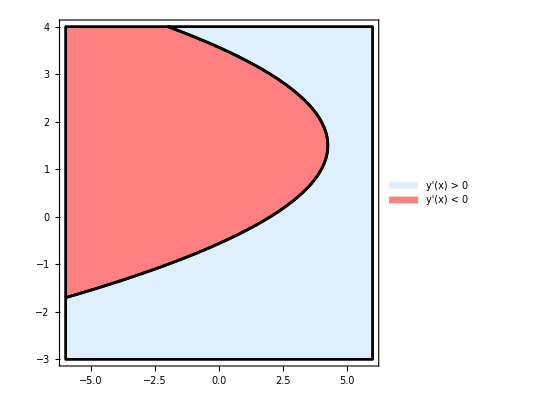

```mathematica
RegionPlot[{y^2-3 y+x-2>0,y^2-3 y+x-2<0},
{x,-6,6},{y,-3,4},
BoundaryStyle -> {Black, Thin},
PlotStyle->{LightBlue,Pink},
PlotLegends->{"y'(x) > 0","y'(x) < 0"}
]
```

## Завдання 1 пункт 4

y^2 - 3y + x - 2 = 0

Точка максимума задовольняє наступні умови  та 
 АЛЕ згадуючи першу умову [ ] матимемо, 
а 1 > 0 завжди, отже у нас не буде локальних максимумів.

## Завдання 1 пункт 5

Опуклість (вгору/вниз) задається знаком другої похідної, тобто y(x) опукла догори якщо  та опукла донизу якщо  
в попередньому пункті ми вже визначили що , отже залишилось лише це задати через функцію RegionPlot

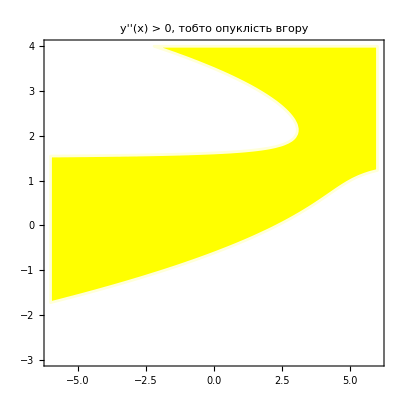

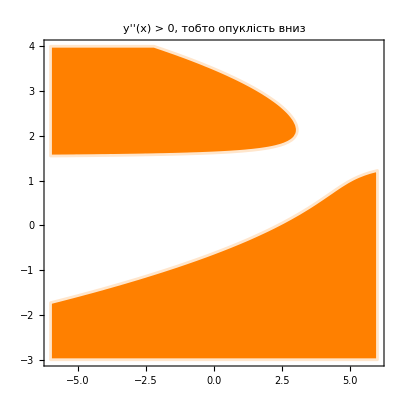

```mathematica
g[x_,y_]:=1+(2 y-3) (y^2-3 y+x-2);

RegionPlot[g[x,y]>0,
{x,-6,6},{y,-3,4},
BoundaryStyle -> {LightYellow},
PlotStyle->{Yellow}
,PlotLabel->" y''(x) > 0, тобто опуклість вгору "]

RegionPlot[g[x,y]<0,
{x,-6,6},{y,-3,4},
BoundaryStyle -> {LightOrange},
PlotStyle->{Orange},
PlotLabel->" y''(x) > 0, тобто опуклість вниз"]
```

## Завдання 1 пункт 6

Точки перегину - точки де =0	=>		 =>
=>	 = -1  	=>	 	 =>	 x = 
Але щоб це зобразити достатньо використати функцію ContourPlot

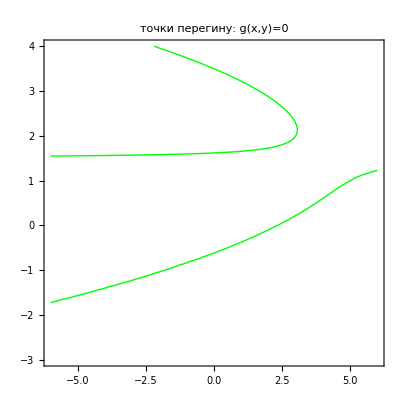

```mathematica
ContourPlot[1+(2 y-3) (y^2-3 y+x-2)==0,{x,-6,6},
{y,-3,4},
ContourStyle->{Thick,Green},
PlotLabel->"точки перегину: g(x,y)=0"
]
```

## Завдання 1 пункт 7

Тут будемо використовувати функцію NDSolve для наближеного розв’язку рівнянь в даних точках,

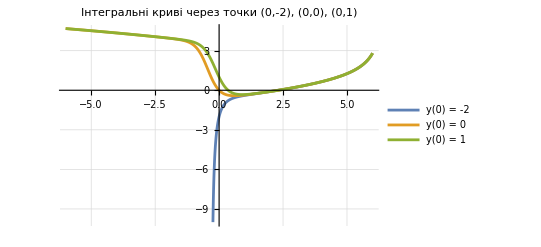

```mathematica
sol1=NDSolve[{y'[x]==y[x]^2-3*y[x]+x-2,y[0]==-2},y,{x, -0.32, 6}];
sol2=NDSolve[{y'[x]==y[x]^2-3*y[x]+x-2,y[0]==0},y,{x, -6, 6}];
sol3=NDSolve[{y'[x]==y[x]^2-3*y[x]+x-2,y[0]==1},y,{x, -6, 6}];

Plot[Evaluate[{y[x]/. sol1,y[x]/. sol2,y[x]/. sol3}],
{x,-6,6},
PlotRange->{{8, -8}, {10, -10}},
GridLines->Automatic,
PlotLabel->"Інтегральні криві через точки (0,-2), (0,0), (0,1)",
PlotLegends-> {"y(0) = -2", "y(0) = 0", "y(0) = 1"}
]
```

## Завдання 2 пункт 1

g(y) = y^2 + 3y+ 2. Потрібно зобразити векторне поле

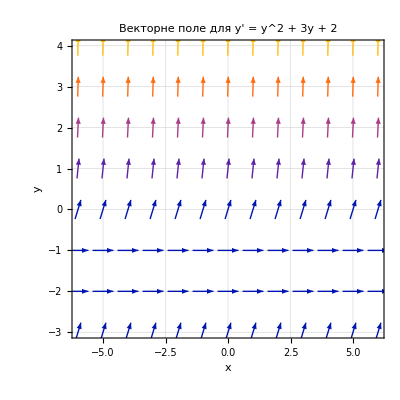

```mathematica
g[y_] := y^2 + 3 y + 2;

VectorPlot[
 {1, g[y]},
 {x, -6, 6}, {y, -3, 4},
 VectorPoints -> Flatten[Table[{x, y}, {x, -6, 6, 1}, {y, {-4, -3, -2, -1, 0, 1, 2, 3, 4}}], 1],
 VectorScale -> {Small, Scaled[0.5], None},
 AxesLabel -> {"x", "y"},
 PlotLabel -> "Векторне поле для y' = y^2 + 3y + 2",
 GridLines -> Automatic
]
```

## Завдання 2 пункт 2

=>  => 

точки спадання ; зростання y^2 + 3y+ 2 > 0
точки перегину =>   =>  =>  =>

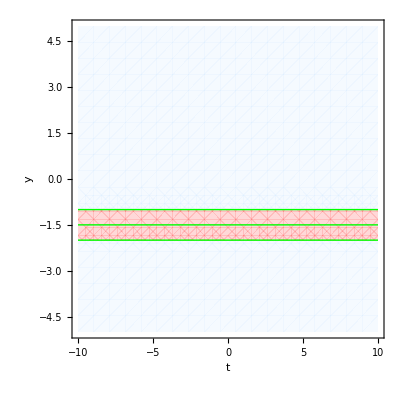

```mathematica
g[y_] := y^2 + 3 y + 2


(* Область зростання: g(y) > 0 (голубий фон) *)
regionIncrease = RegionPlot[g[y] > 0, {t, -10, 10}, {y, -5, 5},
  PlotStyle -> {LightBlue, Opacity[0.3]}, BoundaryStyle -> None];

(* Область спадання: g(y) < 0 (рожевий фон) *)
regionDecrease = RegionPlot[g[y] < 0, {t, -10, 10}, {y, -5, 5},
  PlotStyle -> {Pink, Opacity[0.3]}, BoundaryStyle -> None];

(* Множина точок перегину: розв'язок (2y+3)(y^2+3y+2)=0, тобто y = -2, -3/2, -1 *)
inflectionLines = Graphics[{Green, Thick,
   Line[{{-10, -2}, {10, -2}}],
   Line[{{-10, -3/2}, {10, -3/2}}],
   Line[{{-10, -1}, {10, -1}}]}];


Show[regionIncrease, regionDecrease, inflectionLines,
  PlotRange -> {{-10, 10}, {-5, 5}},
  Axes -> True,
  AxesLabel -> {"t", "y"}]
```

## Завдання 2 пункт 3

знайдемо розв’язок
  =>   =>  =>  =>  = x+C =>    =>  
Розв’яжемо рівняння коші 
 =>   =>  => 
Отже розв’язком буде
 = 
Асимптоти
рівняння вироджується коли знаменник = 0, тобто  =>  =>  це і буде рівнянням асимптоти коли   ну тобто х дійсний це буде  ( та  >0) або (  та ). Тобто

## Завдання 2 пункт 4

Як ми вже дізналися вище -1, -2 є розв’язками g(y), отже , ,

```mathematica
ClearAll["Global`*"];

ySol[x_, y0_] := (2 (y0 + 1) Exp[x] - (y0 + 2)) / ((y0 + 2) - (y0 + 1) Exp[x]);

xMin = -2; 
xMax = 2;

(* ========== 1. y0 \in (-∞, -2) ========== *)
y0Region1 = {-3, -4, -10};

plotRegion1 = Plot[
  Evaluate@Table[ySol[x, y0], {y0, y0Region1}],
  {x, xMin, xMax},
  PlotRange -> All,
  PlotLegends -> Table["y0 = " <> ToString[y0], {y0, y0Region1}],
  PlotLabel -> "Розв'язки для y0 < -2",
  AxesLabel -> {"x", "y(x, y0)"}
];

(* ========== 2. y0 \in [-2, -1] ========== *)
y0Region2 = {-2, -1.5, -1.2, -1};

plotRegion2 = Plot[
  Evaluate@Table[ySol[x, y0], {y0, y0Region2}],
  {x, xMin, xMax},
  PlotRange -> All,
  PlotLegends -> Table["y0 = " <> ToString[y0], {y0, y0Region2}],
  PlotLabel -> "Розв'язки для -2 ≤ y0 ≤ -1",
  AxesLabel -> {"x", "y(x, y0)"}
];

(* ========== 3. y0 \in (-1, +∞) ========== *)
y0Region3 = {0, 1, 2, 3};

plotRegion3 = Plot[
  Evaluate@Table[ySol[x, y0], {y0, y0Region3}],
  {x, xMin, xMax},
  PlotRange -> All,
  PlotLegends -> Table["y0 = " <> ToString[y0], {y0, y0Region3}],
  PlotLabel -> "Розв'язки для y0 > -1",
  AxesLabel -> {"x", "y(x, y0)"}
];


(*GraphicsRow[{plotRegion1, plotRegion2, plotRegion3}, ImageSize -> Large]*)
GraphicsRow[{plotRegion1}, ImageSize -> Large]
GraphicsRow[{plotRegion2}, ImageSize -> Large]
GraphicsRow[{plotRegion3}, ImageSize -> Large]
```

-Graphics-

-Graphics-

-Graphics-

## Завдання 2 пункт 5

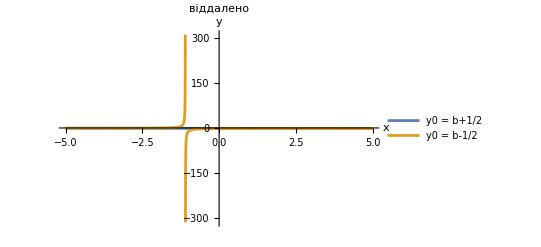

-Graphics-

```mathematica
b = -2; 

gr1 = Plot[
   {ySol[x, b + 0.5], ySol[x, b - 0.5]},
   {x, -5, 5},
   PlotRange -> All,
   PlotLegends -> {"y0 = b+1/2", "y0 = b-1/2"},
   AxesLabel -> {"x", "y"},
   PlotLabel-> "віддалено"
];


Show[gr1]

y1[x_] := -(2 Exp[x] + 1)/(1 + Exp[x]);
y2[x_] := (6 Exp[x] - 1)/(1 - 3 Exp[x]);

Plot[{y1[x], y2[x]}, {x, 0, 5}, PlotRange->All, 
     PlotLabels->{"y(x, -1.5)", "y(x, -2.5)"},
      PlotLabel-> "приближено",
      AxesLabel->{"x","y"}
      ]
```

Тут двома різними способами знайдемо x, такий що

```mathematica
diff[x_] := y1[x] - y2[x];

NSolve[ Abs[diff[x]] == 10^-3 && x>=0, x, Reals]

FindRoot[ Abs[diff[x]] - 10^-3, {x, 2}]
```

{{x→7.19494}}

{x→7.19494}